```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/robyn/Documents/Research/KLStats/Isochrone/With4MOSTErrors/RedGiants

```mathematica
<<streams10x5000.mx
```

Conversion factor between km/s and kpc/Myr to a zillion (16) sigfigs

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

Define the “true” potential

```mathematica
Phi[r_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])
PhiEff[r_,L_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])+L^2/(2 r^2)
vcirc[r_,M_,b_]:=Sqrt[(M r^2)/(Sqrt[b^2+r^2] (b+Sqrt[b^2+r^2])^2)]
```

```mathematica
Jr[r_,pr_,L_,M_,b_]:=M/Sqrt[-pr^2-L^2/r^2+2 M/(b+Sqrt[b^2+r^2])]-1/2 (L+Sqrt[L^2+4 M b]/2)
```

Color point plots

```mathematica
ListColorPlot[x_,y_,c_,csize_,cscl_,xlab_,ylab_]:=Show[Graphics[Flatten[MapThread[{ColorData[cscl][(#3-Min[c])/(Max[c]-Min[c])],Disk[{#1,#2},csize]}&,{x,y,c}]]],Frame->True,FrameStyle->Directive[FontFamily->"Helvetica",FontSize->20],FrameLabel->{xlab,ylab}]
```

Annotation for the color plot - shows a color bar

```mathematica
PlotAnnotate[M_,b_,crange_,dc_,label_]:=Graphics[{Style[Text["M = "<>ToString[M]<>" \!\(\*SuperscriptBox[\(kpc\), \(3\)]\)\!\(\*SuperscriptBox[\(Myr\), \(-2\)]\), b="<>ToString[b]<>" kpc",Scaled[{0.02,0.98}],{-1,1}],TextAlignment->-1,FontFamily->"Helvetica",FontSize->18],MyColorBar[crange,dc,label][[1]]}]

α=0.9;(*total scaled width of color bar*)
β=0.05;(*scaled offset from the left end of the plot*)
γ=0.05;(*scaled distance of the bottom of the bar from the bottom of the plot*)
δγ=0.03;(*scaled height of color bar*)MyColorBar[crange_,dc_,label_]:=Graphics[Flatten[{Black,Style[Text[label,Scaled[{β/2,γ+δγ/2}]],FontFamily->"Helvetica",FontSize->14],Table[{ColorData["Rainbow"][(c-crange[[1]])/(crange[[2]]-crange[[1]])],Rectangle[Scaled[{α (c-crange[[1]])/(crange[[2]]+dc-crange[[1]])+β,γ}],Scaled[{α (c-crange[[1]]+dc)/(crange[[2]]+dc-crange[[1]])+β,γ+δγ}]],Black,Style[Text[Round[c,dc],Scaled[{α (c-crange[[1]]+dc/2)/(crange[[2]]+dc-crange[[1]])+β,γ+1.75 δγ}]],FontFamily->"Helvetica",FontSize->14]},{c,crange[[1]],crange[[2]],dc}]}]]
```

```mathematica
MyColorBar[{0,10},1,"J_r"]
```

Examine distances from the Sun to the stream stars

```mathematica
trueDists=Sqrt[(truePositions[[All,1]]-8)^2+truePositions[[All,2]]^2+truePositions[[All,3]]^2];
```

```mathematica
dbins=Table[id,{id,0,80,1}];
dcounts=BinCounts[trueDists,{dbins}];
```

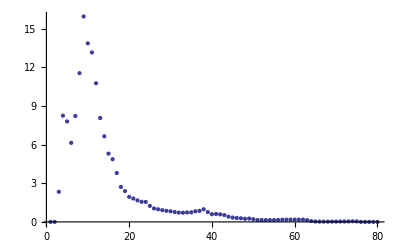

```mathematica
ListPlot[Transpose[{dbins[[2;;Length[dbins]]],dcounts/(dbins[[2;;Length[dbins]]]^2)}],PlotRange->All]
```

Convert (x,v) to observables, convolve with errors, and convert back to (x’,v’)

NOTE: make sure that these four filenames are the same in here and in data_realization_gaia.f!!!!

```mathematica
fnamePosIn="pos.test.dat"
fnamePosOut="newpos.test.dat"
fnameVelIn="vel.test.dat"
fnameVelOut="newvel.test.dat"
fnameObsOut="obs.dat"
```

pos.test.dat

newpos.test.dat

vel.test.dat

newvel.test.dat

obs.dat

```mathematica
pStream=OpenWrite[fnamePosIn,BinaryFormat->False]
vStream=OpenWrite[fnameVelIn,BinaryFormat->False]
```

OutputStream[pos.test.dat,145]

OutputStream[vel.test.dat,146]

```mathematica
Write[pStream,Length[truePositions]];
Export[pStream,truePositions,"Data"];
Export[vStream,trueVelocities,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.test.dat

vel.test.dat

## At this point, manually run data_realizations_gaia

```mathematica
pStream=OpenRead[fnamePosOut];
vStream=OpenRead[fnameVelOut];
oStream=OpenRead[fnameObsOut];
n1=Read[pStream,Number]
n2=Read[oStream,Number]
Dimensions[convPositions=ReadList[pStream,{Number,Number,Number}]]
Dimensions[convVelocities=ReadList[vStream,{Number,Number,Number}]]
Dimensions[convObs=ReadList[oStream,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}]]
Close[pStream];
Close[vStream];
Close[oStream];
```

50000

50000

{50000,3}

{50000,3}

{50000,11}

columns of observational file are vmag, alpha, delta, parallax, par error, mu_alpha, pm error, mu_delta, pm error, RV, RV error

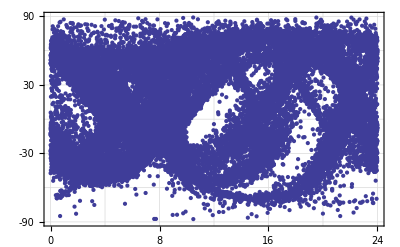

```mathematica
ListPlot[Transpose[{convObs[[All,2]]*24/(2π),convObs[[All,3]]/Degree}],PlotRange->{{0,24},{-90,90}},Frame->True,FrameTicks->{Range[0,24,4],Range[-90,90,30],None,None},GridLines->{Range[0,24,4],Range[-90,90,30]}]
```

Data quality cuts (on observational data)

### Histogram of magnitudes - cut out V>20

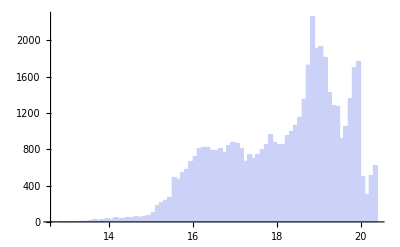

```mathematica
Histogram[convObs[[All,1]]]
```

```mathematica
Tally[magSel=Thread[convObs[[All,1]]<20]]
```

{{True,48072},{False,1928}}

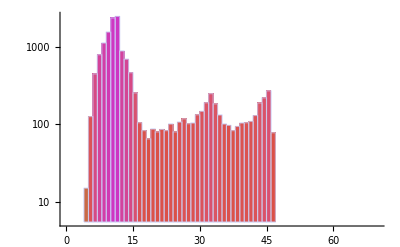

```mathematica
Show[Histogram[trueDists,{0,70,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel]],{0,70,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

### Cut out negative parallaxes, and those with huge errors

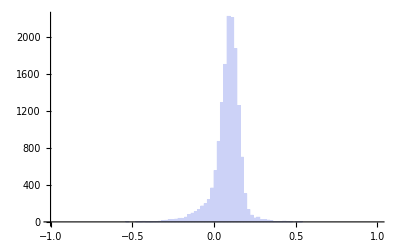

```mathematica
Histogram[convObs[[All,4]],{-1,1,.02}]
```

```mathematica
Tally[posParSel=Thread[Thread[(convObs[[All,4]]>1*^-5)]&&Thread[(convObs[[All,4]]<10)]]]
```

{{True,48072},{False,1928}}

```mathematica
pars=Pick[convObs[[All,4]],posParSel];
```

```mathematica
pars[[Ordering[pars,-50]]]
```

{0.327938,0.327994,0.329857,0.330701,0.33088,0.331679,0.331911,0.335652,0.339211,0.339416,0.339823,0.340028,0.340075,0.340311,0.342495,0.34381,0.345082,0.345452,0.345637,0.347707,0.348615,0.350775,0.353424,0.355302,0.357447,0.363481,0.375603,0.377096,0.381029,0.385461,0.394306,0.400723,0.406589,0.416263,0.422559,0.430812,0.432041,0.434853,0.438074,0.438484,0.438963,0.443473,0.443565,0.445678,0.456237,0.470945,0.470957,0.500257,0.506588,0.524528}

Histogram::hbins: The bin specification {"Log", {-5, 0, 0.1}} cannot be used to determine either how many or which bins to use.

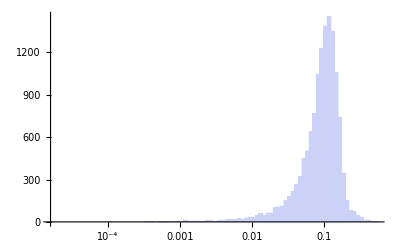

```mathematica
Histogram[Pick[convObs[[All,4]],posParSel],{"Log",{-5,0,0.1}}]
```

```mathematica
Tally[hugeParErrSel=Thread[Abs[convObs[[All,5]]]< 1000]]
```

{{True,48072},{False,1928}}

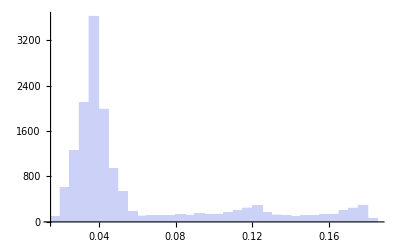

```mathematica
Histogram[Pick[convObs[[All,5]],hugeParErrSel],PlotRange->All]
```

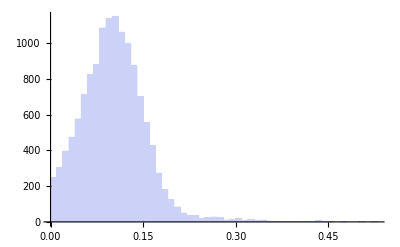

```mathematica
Histogram[Pick[convObs[[All,4]],Thread[posParSel&&hugeParErrSel]],PlotRange->All]
```

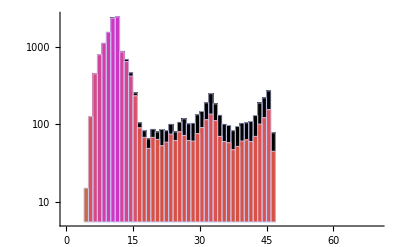

```mathematica
Show[Histogram[trueDists,{0,70,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel]],{0,70,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

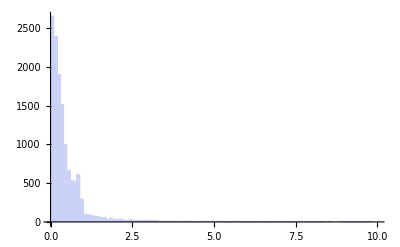

```mathematica
Histogram[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]],{0,10,0.1}]
```

```mathematica
Log10[Max[trueDists]]
```

1.66719

```mathematica
Log10[Min[trueDists]]
```

0.653211

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{Log10[Min[trueDists]],Log10[Max[trueDists]]},0.2,"[D]"]]
```

-Graphics-

```mathematica
Min[Log10[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]]]]
```

-4.25026

```mathematica
Max[Log10[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]]]]
```

3.21689

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Abs[Pick[((1/convObs[[All,4]])-trueDists)/trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]]],1,"Rainbow","RA","Dec"],MyColorBar[{-4.25,3.25},0.25,"σ_D/D"]]
```

-Graphics-

```mathematica
Log10[Min[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]]]]
```

-1.15366

```mathematica
Log10[Max[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]]]]
```

3.95239

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{-1.15,4.0},0.5,"σ_π/π"]]
```

-Graphics-

### Dataquality cut on parallaxes

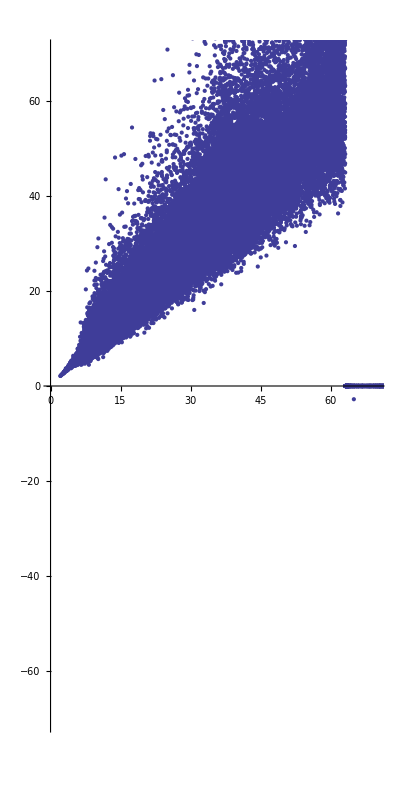

```mathematica
ListPlot[Transpose[{trueDists,1/convObs[[All,4]]}],PlotRange->{{0,70},{-70,70}},AspectRatio->2]
```

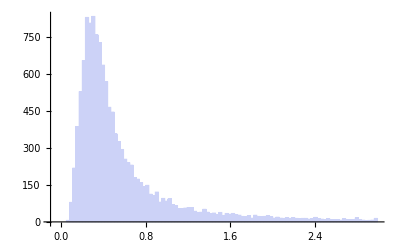

```mathematica
Histogram[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[magSel&&posParSel&&hugeParErrSel]],{-.1,3,.03}]
```

```mathematica
Tally[dqParSel=Thread[Abs[convObs[[All,5]]/convObs[[All,4]]]<0.2]]
```

{{True,24529},{False,25471}}

```mathematica
Dimensions[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]
```

{24529}

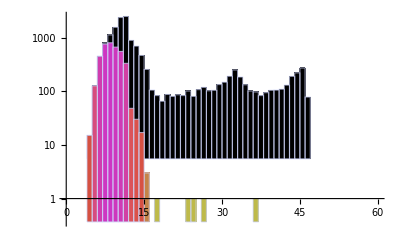

```mathematica
Show[Histogram[trueDists,{0,60,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]],{0,60,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

```mathematica
Min[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

0.32703

```mathematica
Max[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

1.06942

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel]]/Degree,Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{Log10[Min[trueDists]],Log10[Max[trueDists]]},0.2,"[D]"]]
```

-Graphics-

```mathematica
Min[Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

0.653211

```mathematica
Max[Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

1.5677

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Log10[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{0.65,1.6},0.1,"[D]"]]
```

-Graphics-

```mathematica
Min[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

0.32703

```mathematica
Max[Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]]]
```

1.06942

```mathematica
Show[ListColorPlot[Pick[convObs[[All,2]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Pick[convObs[[All,3]],Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]/Degree,Log10[Pick[(1/convObs[[All,4]]),Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel]]],1,"Rainbow","RA","Dec"],MyColorBar[{0.3,1.1},0.1,"[1/π]"]]
```

-Graphics-

### Dataquality cut on proper motions is basically the same as for pars - errors are proportional

### Dataquality cut on RVs

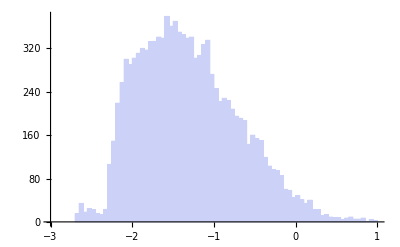

```mathematica
Histogram[Log10[convObs[[All,11]]/convObs[[All,10]]],{-3,1,.05}]
```

```mathematica
Tally[dqRVSel=Thread[Abs[convObs[[All,11]]]<10]]
```

{{True,48072},{False,1928}}

```mathematica
45787
```

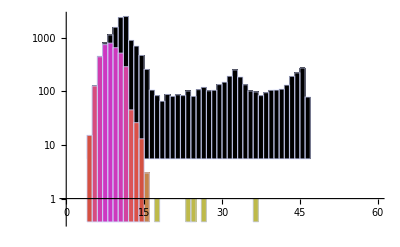

```mathematica
Show[Histogram[trueDists,{0,60,1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[Pick[trueDists,Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel&&dqRVSel]],{0,60,1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

### Combining all the cuts together

```mathematica
Tally[allSels=Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel&&dqRVSel]]
```

{{True,24529},{False,25471}}

```mathematica
Dimensions[tpSel=Pick[truePositions,allSels]]
```

{24529,3}

```mathematica
Dimensions[cpSel=Pick[convPositions,allSels]]
```

{24529,3}

```mathematica
Dimensions[tvSel=Pick[trueVelocities,allSels]]
```

{24529,3}

```mathematica
Dimensions[cvSel=Pick[convVelocities,allSels]]
```

{24529,3}

### Plots examining error behavior etc

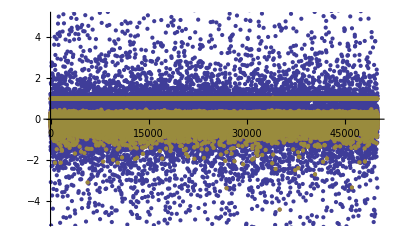

```mathematica
ListPlot[Transpose[(truePositions-convPositions)/truePositions],PlotRange->{-5,5}]
```

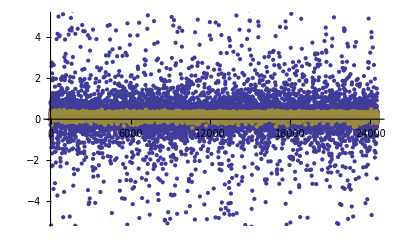

```mathematica
ListPlot[Transpose[(tpSel-cpSel)/tpSel],PlotRange->{-5,5}]
```

```mathematica
convDists=Sqrt[(convPositions[[All,1]]-8)^2+convPositions[[All,2]]^2+convPositions[[All,3]]^2];
```

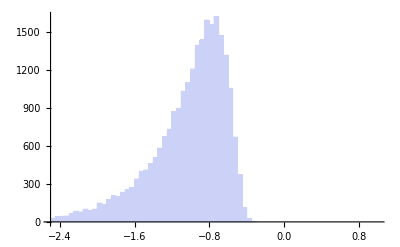

```mathematica
Histogram[Pick[Log10[Abs[(trueDists-convDists)]/trueDists],allSels],{-2.5,1,0.05}]
```

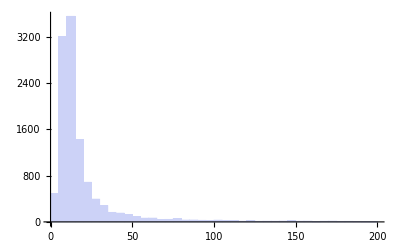

```mathematica
Histogram[Pick[convDists,Thread[!allSels]],{0,200,5}]
```

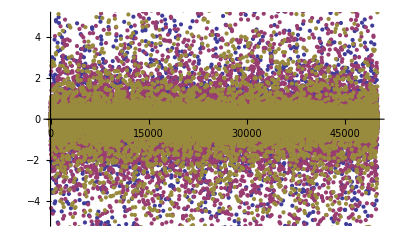

```mathematica
ListPlot[Transpose[(trueVelocities-convVelocities)/trueVelocities],PlotRange->{-5,5}]
```

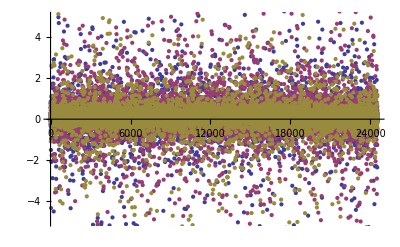

```mathematica
ListPlot[Transpose[(tvSel-cvSel)/tvSel],PlotRange->{-5,5}]
```

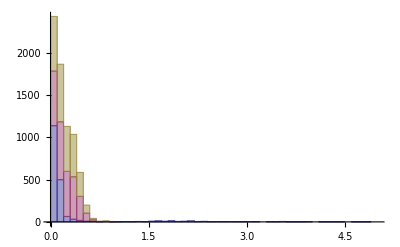

```mathematica
Histogram[Transpose[(tpSel-cpSel)/tpSel],{0,5,.1},ChartLayout->"Stacked"]
```

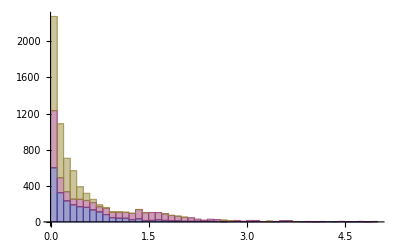

```mathematica
Histogram[Transpose[(tvSel-cvSel)/tvSel],{0,5,.1},ChartLayout->"Stacked"]
```

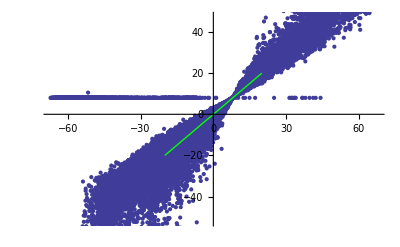

```mathematica
Show[ListPlot[Transpose[{truePositions[[All,1]],convPositions[[All,1]]}]],Plot[x,{x,-20,20},PlotStyle->Directive[Thick,Green]]]
```

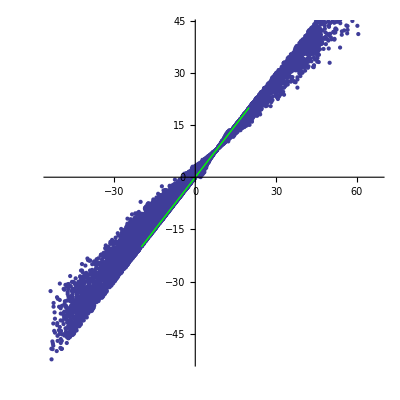

```mathematica
Show[ListPlot[Transpose[{tpSel[[All,1]],cpSel[[All,1]]}],AspectRatio->1],Plot[x,{x,-20,20},PlotStyle->Directive[Thick,Green]]]
```

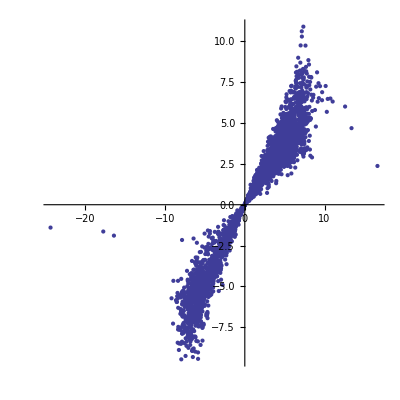

```mathematica
ListPlot[Transpose[{tpSel[[All,2]],cpSel[[All,2]]}],AspectRatio->1]
```

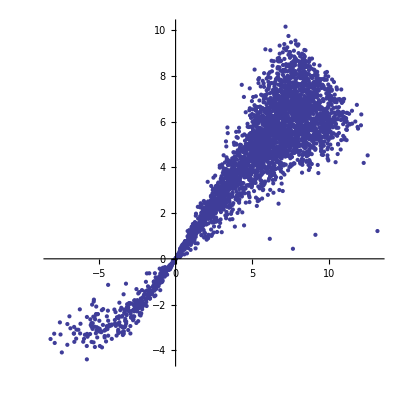

```mathematica
ListPlot[Transpose[{tpSel[[All,3]],cpSel[[All,3]]}],AspectRatio->1]
```

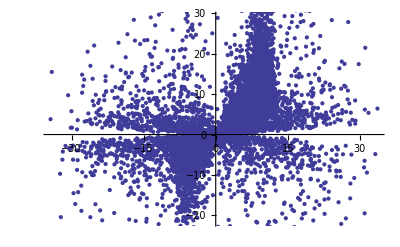

```mathematica
ListPlot[Transpose[{truePositions[[All,3]],convPositions[[All,3]]}]]
```

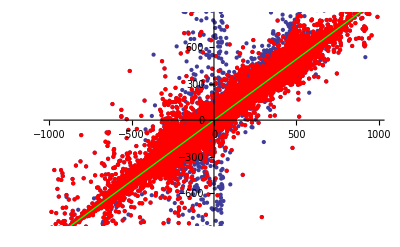

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,1]],convVelocities[[All,1]]}]],ListPlot[Transpose[{tvSel[[All,1]],cvSel[[All,1]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

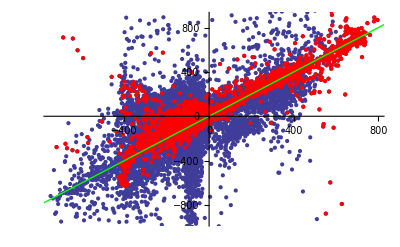

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,2]],convVelocities[[All,2]]}]],ListPlot[Transpose[{tvSel[[All,2]],cvSel[[All,2]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

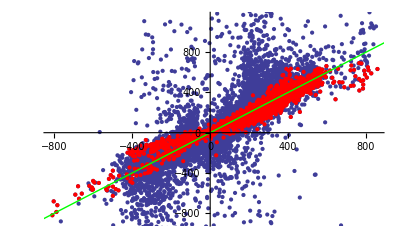

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,3]],convVelocities[[All,3]]}]],ListPlot[Transpose[{tvSel[[All,3]],cvSel[[All,3]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

Convert (x’,v’) to (Jr’,L’,Lz’)

```mathematica
fnameCleanPosIn="pos.clean.dat"
fnameCleanVelIn="vel.clean.dat"
```

pos.clean.dat

vel.clean.dat

```mathematica
pStream=OpenWrite[fnameCleanPosIn,BinaryFormat->False]
vStream=OpenWrite[fnameCleanVelIn,BinaryFormat->False]
```

OutputStream[pos.clean.dat,58]

OutputStream[vel.clean.dat,59]

```mathematica
Write[pStream,Length[cpSel]];
Export[pStream,cpSel,"Data"];
Export[vStream,cvSel,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.clean.dat

vel.clean.dat

```mathematica
link=Install["/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math"]
```

LinkObject[/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math,20170,12]

```mathematica
Mtrial=12.2;
btrial=8.0;
```

```mathematica
Dimensions[convJ=Table[{0,0,0},{i,1,Length[cpSel]}]]
```

{24529,3}

```mathematica
For[i=1,i≤Length[cpSel],i++,convJ[[i]]=CartToAA[Mtrial,btrial,cpSel[[i]],cvSel[[i]]];];
```

Some stuff has unbound orbits, so select those out

```mathematica
Tally[boundSel=Thread[convJ[[All,3]]>0]]
```

{{True,24518},{False,11}}

```mathematica
Dimensions[convJbound=Pick[convJ,boundSel]]
```

{24518,3}

```mathematica
Dimensions[tJSel=Pick[Pick[trueActions,allSels],boundSel]]
```

{24518,3}

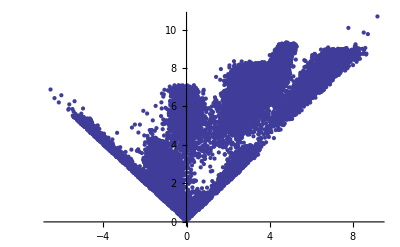

```mathematica
ListPlot[convJbound[[All,{1,2}]]]
```

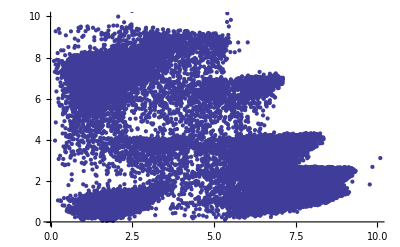

```mathematica
ListPlot[convJbound[[All,{2,3}]],PlotRange->{{0,10},{0,10}}]
```

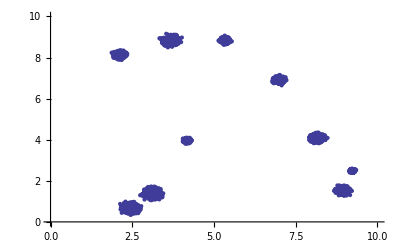

```mathematica
ListPlot[tJSel[[All,{2,3}]],PlotRange->{{0,10},{0,10}}]
```

```mathematica
ListPointPlot3D[convJbound]
```

-Graphics3D-

```mathematica
Show[ListPlot[Transpose[{tJSel[[All,3]],convJbound[[All,3]]}],PlotRange->{{0,15},{0,15}},AspectRatio->1],Plot[x,{x,0,15}]]
```

-Graphics-

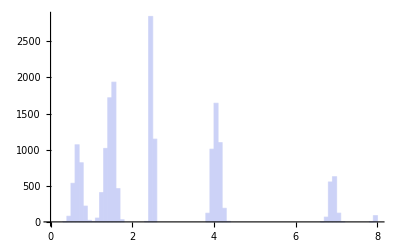

```mathematica
Histogram[tJSel[[All,3]],{0,8,.1}]
```

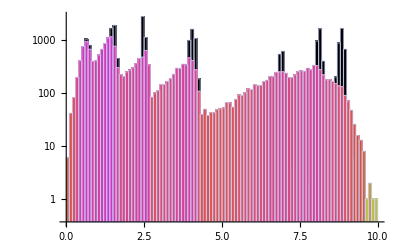

```mathematica
Show[Histogram[tJSel[[All,3]],{0,10,.1},{"Log","Count"},ColorFunction->Function[{x},Black]],Histogram[convJbound[[All,3]],{0,10,.1},{"Log","Count"},ColorFunction->"NeonColors"]]
```

```mathematica
ListPlot[Transpose[{tJSel[[All,2]],convJbound[[All,2]]}],PlotRange->{{0,15},{0,15}},AspectRatio->1]
```

-Graphics-

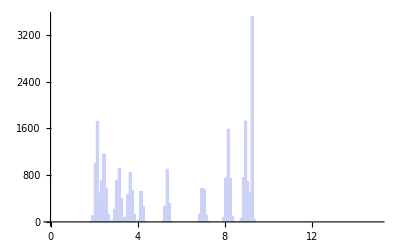

```mathematica
Histogram[tJSel[[All,2]],{0,15,.1}]
```

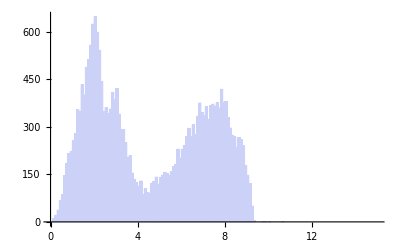

```mathematica
Histogram[convJbound[[All,2]],{0,15,.1}]
```

```mathematica
ListPlot[Transpose[{tJSel[[All,1]],convJbound[[All,1]]}],PlotRange->{{-10,10},{-10,10}},AspectRatio->1]
```

-Graphics-

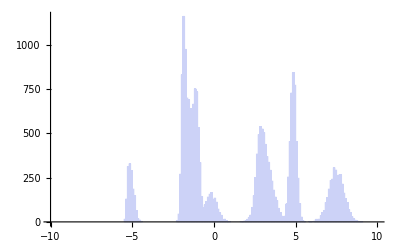

```mathematica
Histogram[tJSel[[All,1]],{-10,10,.1}]
```

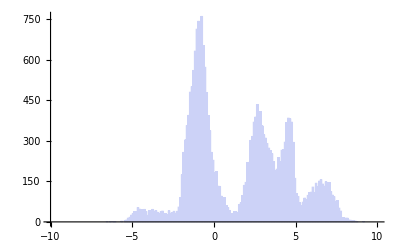

```mathematica
Histogram[convJbound[[All,1]],{-10,10,.1}]
```

Explore param space and generate KL map

```mathematica
Mtrial=12.5;
btrial=8.0;
```

```mathematica
Timing[trialActions=MapThread[CartToAA[(10^Mtrial)/toSolarMasses, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]]
```

{6.06321,0.494659}

```mathematica
logMt0=11.5;
bt0=1.0;
dlogM=0.2;
db=0.5;
logMtMax=14.5;
btMax=20.0;
```

```mathematica
(logMtMax-logMt0)/dlogM
```

15.

```mathematica
btrial=8.0;
```

```mathematica
ParallelEvaluate[Install["/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math"]]
```

{LinkObject[/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math,28,4],LinkObject[/Users/robyn/Documents/Research/KLStats/Isochrone/cartToAA/cartToAA_math,28,4]}

```mathematica
Mscan=ParallelTable[{Mtrial,trialActions=MapThread[CartToAA[(10^Mtrial)/toSolarMasses, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,logMt0,logMtMax,dlogM},Method->"CoarsestGrained"]
```

{{11.5,0},{11.7,0},{11.9,0.0786558},{12.1,0.133301},{12.3,0.291092},{12.5,0.444695},{12.7,0.284848},{12.9,0.224507},{13.1,0.21901},{13.3,0.224677},{13.5,0.227121},{13.7,0.229875},{13.9,0.237701},{14.1,0.247783},{14.3,0.25365},{14.5,0.259095}}

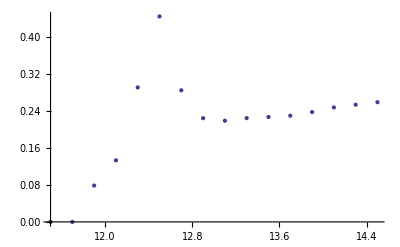

```mathematica
ListPlot[Mscan]
```

```mathematica
Mtrial=Log10[12.2 toSolarMasses]
```

12.4331

```mathematica
logMt0=11.5;
bt0=5.0;
dlogM=0.2;
db=1.0;
logMtMax=14.5;
btMax=20.0;
```

```mathematica
(btMax-bt0)/db
```

15.

```mathematica
bscan=ParallelTable[{btrial,trialActions=MapThread[CartToAA[(10^Mtrial)/toSolarMasses, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{btrial,bt0,btMax,db},Method->"CoarsestGrained"]
```

$Aborted

```mathematica
ListPlot[bscan]
```

```mathematica
DumpSave["KL1DScans.mx",{Mscan,bscan}]
```

```mathematica
logMt0=11.5;
bt0=1.0;
dlogM=0.1;
db=0.5;
logMtMax=14.5;
btMax=20.0;
```

```mathematica
((logMtMax-logMt0)/dlogM)((btMax-bt0)/db)*8.0/1.2/60
```

126.667

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[(10^Mtrial)/toSolarMasses, btrial, #1,#2]&,{cpSel,cvSel}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Length[cpSel]/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample=nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,logMt0,logMtMax,dlogM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{2249.47,{1209,3}}

```mathematica
DumpSave["KL10x5000logM2D.mx",KLStats]
```

{{{11.5,1.,0.240602},{11.5,1.5,0.228},{11.5,2.,0.208757},{11.5,2.5,0},{11.5,3.,0},{11.5,3.5,0},{11.5,4.,0},{11.5,4.5,0},{11.5,5.,0},{11.5,5.5,0},{11.5,6.,0},{11.5,6.5,0},{11.5,7.,0},{11.5,7.5,0},{11.5,8.,0},{11.5,8.5,0},{11.5,9.,0},{11.5,9.5,0},{11.5,10.,0},{11.5,10.5,0},{11.5,11.,0},{11.5,11.5,0},{11.5,12.,0},{11.5,12.5,0},{11.5,13.,0},{11.5,13.5,0},{11.5,14.,0},{11.5,14.5,0},{11.5,15.,0},{11.5,15.5,0},{11.5,16.,0},{11.5,16.5,0},{11.5,17.,0},{11.5,17.5,0},{11.5,18.,0},{11.5,18.5,0},{11.5,19.,0},{11.5,19.5,0},{11.5,20.,0},{11.6,1.,0.238824},{11.6,1.5,0.240444},{11.6,2.,0.235088},{11.6,2.5,0.215119},{11.6,3.,0.189692},{11.6,3.5,0.164792},{11.6,4.,0.155275},{11.6,4.5,0.140245},{11.6,5.,0.128861},{11.6,5.5,0.133343},{11.6,6.,0.120508},{11.6,6.5,0},{11.6,7.,0},{11.6,7.5,0},{11.6,8.,0},{11.6,8.5,0},{11.6,9.,0},{11.6,9.5,0},{11.6,10.,0},{11.6,10.5,0},{11.6,11.,0},{11.6,11.5,0},{11.6,12.,0},{11.6,12.5,0},{11.6,13.,0},{11.6,13.5,0},{11.6,14.,0},{11.6,14.5,0},{11.6,15.,0},{11.6,15.5,0},{11.6,16.,0},{11.6,16.5,0},{11.6,17.,0},{11.6,17.5,0},{11.6,18.,0},{11.6,18.5,0},{11.6,19.,0},{11.6,19.5,0},{11.6,20.,0},{11.7,1.,0.255256},{11.7,1.5,0.241428},{11.7,2.,0.236319},{11.7,2.5,0.242143},{11.7,3.,0.223393},{11.7,3.5,0.193442},{11.7,4.,0.171882},{11.7,4.5,0.145064},{11.7,5.,0.131134},{11.7,5.5,0.122365},{11.7,6.,0.119518},{11.7,6.5,0.118713},{11.7,7.,0.123692},{11.7,7.5,0.121253},{11.7,8.,0.122392},{11.7,8.5,0.118778},{11.7,9.,0.116279},{11.7,9.5,0.11099},{11.7,10.,0.101264},{11.7,10.5,0.103363},{11.7,11.,0.097703},{11.7,11.5,0},{11.7,12.,0},{11.7,12.5,0},{11.7,13.,0},{11.7,13.5,0},{11.7,14.,0},{11.7,14.5,0},{11.7,15.,0},{11.7,15.5,0},{11.7,16.,0},{11.7,16.5,0},{11.7,17.,0},{11.7,17.5,0},{11.7,18.,0},{11.7,18.5,0},{11.7,19.,0},{11.7,19.5,0},{11.7,20.,0},{11.8,1.,0.253456},{11.8,1.5,0.248373},{11.8,2.,0.255158},{11.8,2.5,0.265611},{11.8,3.,0.261471},{11.8,3.5,0.255232},{11.8,4.,0.23956},{11.8,4.5,0.201889},{11.8,5.,0.184132},{11.8,5.5,0.164609},{11.8,6.,0.14469},{11.8,6.5,0.135719},{11.8,7.,0.124345},{11.8,7.5,0.115821},{11.8,8.,0.116663},{11.8,8.5,0.11811},{11.8,9.,0.11805},{11.8,9.5,0.122813},{11.8,10.,0.124117},{11.8,10.5,0.118417},{11.8,11.,0.118809},{11.8,11.5,0.115171},{11.8,12.,0.114375},{11.8,12.5,0.107847},{11.8,13.,0.10029},{11.8,13.5,0.0926263},{11.8,14.,0.0902446},{11.8,14.5,0.0921218},{11.8,15.,0.0861165},{11.8,15.5,0.0879103},{11.8,16.,0.0814312},{11.8,16.5,0.0835914},{11.8,17.,0.0784844},{11.8,17.5,0.081674},{11.8,18.,0},{11.8,18.5,0},{11.8,19.,0},{11.8,19.5,0},{11.8,20.,0},{11.9,1.,0.288515},{11.9,1.5,0.279834},{11.9,2.,0.282367},{11.9,2.5,0.284497},{11.9,3.,0.279428},{11.9,3.5,0.27991},{11.9,4.,0.275729},{11.9,4.5,0.260745},{11.9,5.,0.235121},{11.9,5.5,0.211413},{11.9,6.,0.195793},{11.9,6.5,0.173941},{11.9,7.,0.161038},{11.9,7.5,0.14574},{11.9,8.,0.148165},{11.9,8.5,0.130425},{11.9,9.,0.127048},{11.9,9.5,0.122678},{11.9,10.,0.123102},{11.9,10.5,0.114396},{11.9,11.,0.118063},{11.9,11.5,0.116537},{11.9,12.,0.113669},{11.9,12.5,0.11007},{11.9,13.,0.113128},{11.9,13.5,0.115421},{11.9,14.,0.108101},{11.9,14.5,0.107554},{11.9,15.,0.106925},{11.9,15.5,0.097343},{11.9,16.,0.0919429},{11.9,16.5,0.0936607},{11.9,17.,0.0916762},{11.9,17.5,0.0868388},{11.9,18.,0.0787109},{11.9,18.5,0.0748152},{11.9,19.,0.0775271},{11.9,19.5,0.0687957},{11.9,20.,0.0723698},{12.,1.,0.349246},{12.,1.5,0.344479},{12.,2.,0.32961},{12.,2.5,0.336457},{12.,3.,0.334576},{12.,3.5,0.321414},{12.,4.,0.321684},{12.,4.5,0.303785},{12.,5.,0.281044},{12.,5.5,0.266003},{12.,6.,0.243816},{12.,6.5,0.209581},{12.,7.,0.199231},{12.,7.5,0.177197},{12.,8.,0.165334},{12.,8.5,0.155677},{12.,9.,0.143218},{12.,9.5,0.14055},{12.,10.,0.138352},{12.,10.5,0.127885},{12.,11.,0.132075},{12.,11.5,0.125702},{12.,12.,0.120018},{12.,12.5,0.119496},{12.,13.,0.119057},{12.,13.5,0.118099},{12.,14.,0.11777},{12.,14.5,0.111023},{12.,15.,0.107507},{12.,15.5,0.104404},{12.,16.,0.111054},{12.,16.5,0.104146},{12.,17.,0.103369},{12.,17.5,0.0909821},{12.,18.,0.0927012},{12.,18.5,0.0886281},{12.,19.,0.092949},{12.,19.5,0.0937289},{12.,20.,0.0884524},{12.1,1.,0.468576},{12.1,1.5,0.449281},{12.1,2.,0.420911},{12.1,2.5,0.419599},{12.1,3.,0.408333},{12.1,3.5,0.408399},{12.1,4.,0.399226},{12.1,4.5,0.389494},{12.1,5.,0.366611},{12.1,5.5,0.340191},{12.1,6.,0.295997},{12.1,6.5,0.268189},{12.1,7.,0.238723},{12.1,7.5,0.212476},{12.1,8.,0.1944},{12.1,8.5,0.189651},{12.1,9.,0.177201},{12.1,9.5,0.165302},{12.1,10.,0.16187},{12.1,10.5,0.152101},{12.1,11.,0.142986},{12.1,11.5,0.141096},{12.1,12.,0.140092},{12.1,12.5,0.136503},{12.1,13.,0.13443},{12.1,13.5,0.124553},{12.1,14.,0.121354},{12.1,14.5,0.125792},{12.1,15.,0.119073},{12.1,15.5,0.123392},{12.1,16.,0.116889},{12.1,16.5,0.120695},{12.1,17.,0.121422},{12.1,17.5,0.112293},{12.1,18.,0.1046},{12.1,18.5,0.103453},{12.1,19.,0.10055},{12.1,19.5,0.0987672},{12.1,20.,0.0962862},{12.2,1.,0.495623},{12.2,1.5,0.486895},{12.2,2.,0.497224},{12.2,2.5,0.498804},{12.2,3.,0.512569},{12.2,3.5,0.524764},{12.2,4.,0.531584},{12.2,4.5,0.536875},{12.2,5.,0.534673},{12.2,5.5,0.520044},{12.2,6.,0.479315},{12.2,6.5,0.420648},{12.2,7.,0.368898},{12.2,7.5,0.327294},{12.2,8.,0.292131},{12.2,8.5,0.254737},{12.2,9.,0.234967},{12.2,9.5,0.212342},{12.2,10.,0.200232},{12.2,10.5,0.189277},{12.2,11.,0.175894},{12.2,11.5,0.174062},{12.2,12.,0.163348},{12.2,12.5,0.15879},{12.2,13.,0.154868},{12.2,13.5,0.147716},{12.2,14.,0.152081},{12.2,14.5,0.139439},{12.2,15.,0.137094},{12.2,15.5,0.137402},{12.2,16.,0.129398},{12.2,16.5,0.122302},{12.2,17.,0.120447},{12.2,17.5,0.122969},{12.2,18.,0.122009},{12.2,18.5,0.118666},{12.2,19.,0.113792},{12.2,19.5,0.11123},{12.2,20.,0.113718},{12.3,1.,0.420953},{12.3,1.5,0.428639},{12.3,2.,0.448794},{12.3,2.5,0.453858},{12.3,3.,0.473743},{12.3,3.5,0.491699},{12.3,4.,0.511504},{12.3,4.5,0.540965},{12.3,5.,0.565384},{12.3,5.5,0.60437},{12.3,6.,0.635741},{12.3,6.5,0.642831},{12.3,7.,0.621628},{12.3,7.5,0.552137},{12.3,8.,0.470704},{12.3,8.5,0.422462},{12.3,9.,0.376583},{12.3,9.5,0.338101},{12.3,10.,0.302284},{12.3,10.5,0.267492},{12.3,11.,0.239937},{12.3,11.5,0.230792},{12.3,12.,0.218234},{12.3,12.5,0.209207},{12.3,13.,0.190224},{12.3,13.5,0.190642},{12.3,14.,0.185554},{12.3,14.5,0.17411},{12.3,15.,0.171168},{12.3,15.5,0.165639},{12.3,16.,0.156408},{12.3,16.5,0.151729},{12.3,17.,0.147437},{12.3,17.5,0.138576},{12.3,18.,0.137575},{12.3,18.5,0.135849},{12.3,19.,0.125135},{12.3,19.5,0.123995},{12.3,20.,0.125691},{12.4,1.,0.368516},{12.4,1.5,0.366881},{12.4,2.,0.365466},{12.4,2.5,0.368233},{12.4,3.,0.364412},{12.4,3.5,0.373111},{12.4,4.,0.380169},{12.4,4.5,0.39653},{12.4,5.,0.406707},{12.4,5.5,0.445262},{12.4,6.,0.469971},{12.4,6.5,0.517182},{12.4,7.,0.575803},{12.4,7.5,0.672594},{12.4,8.,0.726743},{12.4,8.5,0.687014},{12.4,9.,0.620793},{12.4,9.5,0.546448},{12.4,10.,0.493348},{12.4,10.5,0.448192},{12.4,11.,0.410566},{12.4,11.5,0.362999},{12.4,12.,0.32848},{12.4,12.5,0.292777},{12.4,13.,0.268488},{12.4,13.5,0.258285},{12.4,14.,0.230852},{12.4,14.5,0.22114},{12.4,15.,0.216698},{12.4,15.5,0.203519},{12.4,16.,0.2058},{12.4,16.5,0.199949},{12.4,17.,0.190205},{12.4,17.5,0.177548},{12.4,18.,0.175581},{12.4,18.5,0.169798},{12.4,19.,0.162523},{12.4,19.5,0.15574},{12.4,20.,0.154071},{12.5,1.,0.337982},{12.5,1.5,0.338815},{12.5,2.,0.345345},{12.5,2.5,0.35049},{12.5,3.,0.349324},{12.5,3.5,0.35003},{12.5,4.,0.35678},{12.5,4.5,0.362732},{12.5,5.,0.367815},{12.5,5.5,0.379171},{12.5,6.,0.383531},{12.5,6.5,0.404045},{12.5,7.,0.42911},{12.5,7.5,0.451866},{12.5,8.,0.497898},{12.5,8.5,0.539045},{12.5,9.,0.587082},{12.5,9.5,0.651542},{12.5,10.,0.700093},{12.5,10.5,0.677316},{12.5,11.,0.617809},{12.5,11.5,0.572935},{12.5,12.,0.523408},{12.5,12.5,0.493473},{12.5,13.,0.458636},{12.5,13.5,0.414245},{12.5,14.,0.385138},{12.5,14.5,0.346799},{12.5,15.,0.312814},{12.5,15.5,0.288235},{12.5,16.,0.268252},{12.5,16.5,0.256127},{12.5,17.,0.245133},{12.5,17.5,0.235909},{12.5,18.,0.227995},{12.5,18.5,0.218085},{12.5,19.,0.209897},{12.5,19.5,0.198652},{12.5,20.,0.188982},{12.6,1.,0.323042},{12.6,1.5,0.336172},{12.6,2.,0.349145},{12.6,2.5,0.347163},{12.6,3.,0.352688},{12.6,3.5,0.345737},{12.6,4.,0.351769},{12.6,4.5,0.354087},{12.6,5.,0.347819},{12.6,5.5,0.352918},{12.6,6.,0.358846},{12.6,6.5,0.365509},{12.6,7.,0.37756},{12.6,7.5,0.389398},{12.6,8.,0.397612},{12.6,8.5,0.425158},{12.6,9.,0.455158},{12.6,9.5,0.489096},{12.6,10.,0.52596},{12.6,10.5,0.541648},{12.6,11.,0.565545},{12.6,11.5,0.593686},{12.6,12.,0.616847},{12.6,12.5,0.62157},{12.6,13.,0.596689},{12.6,13.5,0.556885},{12.6,14.,0.519399},{12.6,14.5,0.5082},{12.6,15.,0.497924},{12.6,15.5,0.479275},{12.6,16.,0.442941},{12.6,16.5,0.403227},{12.6,17.,0.375248},{12.6,17.5,0.343124},{12.6,18.,0.321759},{12.6,18.5,0.302838},{12.6,19.,0.287748},{12.6,19.5,0.275703},{12.6,20.,0.258781},{12.7,1.,0.33286},{12.7,1.5,0.339357},{12.7,2.,0.344166},{12.7,2.5,0.348008},{12.7,3.,0.345343},{12.7,3.5,0.343835},{12.7,4.,0.345274},{12.7,4.5,0.346273},{12.7,5.,0.349081},{12.7,5.5,0.341914},{12.7,6.,0.345888},{12.7,6.5,0.338655},{12.7,7.,0.339608},{12.7,7.5,0.351549},{12.7,8.,0.35823},{12.7,8.5,0.366239},{12.7,9.,0.385374},{12.7,9.5,0.401035},{12.7,10.,0.416831},{12.7,10.5,0.451836},{12.7,11.,0.476955},{12.7,11.5,0.489385},{12.7,12.,0.507646},{12.7,12.5,0.521753},{12.7,13.,0.53849},{12.7,13.5,0.54838},{12.7,14.,0.559208},{12.7,14.5,0.569935},{12.7,15.,0.547455},{12.7,15.5,0.530826},{12.7,16.,0.503764},{12.7,16.5,0.487192},{12.7,17.,0.484659},{12.7,17.5,0.478411},{12.7,18.,0.470636},{12.7,18.5,0.454928},{12.7,19.,0.419598},{12.7,19.5,0.390492},{12.7,20.,0.370891},{12.8,1.,0.33532},{12.8,1.5,0.340234},{12.8,2.,0.337834},{12.8,2.5,0.337198},{12.8,3.,0.330803},{12.8,3.5,0.337461},{12.8,4.,0.336781},{12.8,4.5,0.333226},{12.8,5.,0.33204},{12.8,5.5,0.335076},{12.8,6.,0.333344},{12.8,6.5,0.332605},{12.8,7.,0.330463},{12.8,7.5,0.332002},{12.8,8.,0.337034},{12.8,8.5,0.340836},{12.8,9.,0.354421},{12.8,9.5,0.361229},{12.8,10.,0.369103},{12.8,10.5,0.383045},{12.8,11.,0.399162},{12.8,11.5,0.415399},{12.8,12.,0.434175},{12.8,12.5,0.455415},{12.8,13.,0.458973},{12.8,13.5,0.466422},{12.8,14.,0.486996},{12.8,14.5,0.498745},{12.8,15.,0.514095},{12.8,15.5,0.524604},{12.8,16.,0.518667},{12.8,16.5,0.525164},{12.8,17.,0.52593},{12.8,17.5,0.515649},{12.8,18.,0.499102},{12.8,18.5,0.479862},{12.8,19.,0.467335},{12.8,19.5,0.464998},{12.8,20.,0.468315},{12.9,1.,0.339445},{12.9,1.5,0.340954},{12.9,2.,0.337661},{12.9,2.5,0.339394},{12.9,3.,0.333717},{12.9,3.5,0.334714},{12.9,4.,0.331794},{12.9,4.5,0.326173},{12.9,5.,0.330869},{12.9,5.5,0.326428},{12.9,6.,0.329407},{12.9,6.5,0.322257},{12.9,7.,0.326219},{12.9,7.5,0.32118},{12.9,8.,0.313926},{12.9,8.5,0.321507},{12.9,9.,0.32967},{12.9,9.5,0.335734},{12.9,10.,0.338962},{12.9,10.5,0.3527},{12.9,11.,0.361939},{12.9,11.5,0.373048},{12.9,12.,0.390441},{12.9,12.5,0.400659},{12.9,13.,0.409302},{12.9,13.5,0.41896},{12.9,14.,0.428092},{12.9,14.5,0.438286},{12.9,15.,0.443819},{12.9,15.5,0.449286},{12.9,16.,0.454123},{12.9,16.5,0.46957},{12.9,17.,0.481535},{12.9,17.5,0.498442},{12.9,18.,0.49521},{12.9,18.5,0.485184},{12.9,19.,0.48038},{12.9,19.5,0.491319},{12.9,20.,0.480907},{13.,1.,0.333864},{13.,1.5,0.335745},{13.,2.,0.338247},{13.,2.5,0.334668},{13.,3.,0.337135},{13.,3.5,0.333806},{13.,4.,0.334648},{13.,4.5,0.32985},{13.,5.,0.326087},{13.,5.5,0.327239},{13.,6.,0.323245},{13.,6.5,0.316404},{13.,7.,0.321765},{13.,7.5,0.321579},{13.,8.,0.313947},{13.,8.5,0.306633},{13.,9.,0.30838},{13.,9.5,0.313249},{13.,10.,0.311797},{13.,10.5,0.321846},{13.,11.,0.322182},{13.,11.5,0.337582},{13.,12.,0.350105},{13.,12.5,0.358835},{13.,13.,0.37145},{13.,13.5,0.385403},{13.,14.,0.398066},{13.,14.5,0.40532},{13.,15.,0.401009},{13.,15.5,0.412249},{13.,16.,0.415773},{13.,16.5,0.427319},{13.,17.,0.426942},{13.,17.5,0.43504},{13.,18.,0.433132},{13.,18.5,0.442653},{13.,19.,0.45055},{13.,19.5,0.467851},{13.,20.,0.473605},{13.1,1.,0.336133},{13.1,1.5,0.335245},{13.1,2.,0.334945},{13.1,2.5,0.332758},{13.1,3.,0.331226},{13.1,3.5,0.331915},{13.1,4.,0.329179},{13.1,4.5,0.328855},{13.1,5.,0.329646},{13.1,5.5,0.332749},{13.1,6.,0.327835},{13.1,6.5,0.324234},{13.1,7.,0.318367},{13.1,7.5,0.323351},{13.1,8.,0.322303},{13.1,8.5,0.313753},{13.1,9.,0.314218},{13.1,9.5,0.308059},{13.1,10.,0.304038},{13.1,10.5,0.30761},{13.1,11.,0.306898},{13.1,11.5,0.314998},{13.1,12.,0.317581},{13.1,12.5,0.321007},{13.1,13.,0.337293},{13.1,13.5,0.342742},{13.1,14.,0.352813},{13.1,14.5,0.367966},{13.1,15.,0.37857},{13.1,15.5,0.38979},{13.1,16.,0.394018},{13.1,16.5,0.394306},{13.1,17.,0.398975},{13.1,17.5,0.403935},{13.1,18.,0.406421},{13.1,18.5,0.415224},{13.1,19.,0.425511},{13.1,19.5,0.425956},{13.1,20.,0.415185},{13.2,1.,0.330125},{13.2,1.5,0.327157},{13.2,2.,0.330757},{13.2,2.5,0.335402},{13.2,3.,0.329518},{13.2,3.5,0.330569},{13.2,4.,0.33045},{13.2,4.5,0.325792},{13.2,5.,0.327647},{13.2,5.5,0.323318},{13.2,6.,0.319995},{13.2,6.5,0.320887},{13.2,7.,0.325065},{13.2,7.5,0.319295},{13.2,8.,0.319619},{13.2,8.5,0.313772},{13.2,9.,0.313183},{13.2,9.5,0.312776},{13.2,10.,0.311551},{13.2,10.5,0.297295},{13.2,11.,0.299025},{13.2,11.5,0.300379},{13.2,12.,0.304659},{13.2,12.5,0.309159},{13.2,13.,0.312512},{13.2,13.5,0.313963},{13.2,14.,0.324878},{13.2,14.5,0.334941},{13.2,15.,0.336821},{13.2,15.5,0.354346},{13.2,16.,0.362184},{13.2,16.5,0.376099},{13.2,17.,0.385932},{13.2,17.5,0.384944},{13.2,18.,0.389819},{13.2,18.5,0.37628},{13.2,19.,0.380653},{13.2,19.5,0.386939},{13.2,20.,0.395505},{13.3,1.,0.332577},{13.3,1.5,0.331913},{13.3,2.,0.335734},{13.3,2.5,0.331489},{13.3,3.,0.324706},{13.3,3.5,0.332081},{13.3,4.,0.327},{13.3,4.5,0.326068},{13.3,5.,0.326543},{13.3,5.5,0.324337},{13.3,6.,0.323643},{13.3,6.5,0.316114},{13.3,7.,0.316908},{13.3,7.5,0.316326},{13.3,8.,0.310855},{13.3,8.5,0.3133},{13.3,9.,0.313862},{13.3,9.5,0.31337},{13.3,10.,0.311097},{13.3,10.5,0.306248},{13.3,11.,0.304237},{13.3,11.5,0.300701},{13.3,12.,0.298453},{13.3,12.5,0.298959},{13.3,13.,0.299053},{13.3,13.5,0.306432},{13.3,14.,0.310753},{13.3,14.5,0.310715},{13.3,15.,0.316296},{13.3,15.5,0.321754},{13.3,16.,0.328916},{13.3,16.5,0.334393},{13.3,17.,0.350732},{13.3,17.5,0.360779},{13.3,18.,0.366969},{13.3,18.5,0.377919},{13.3,19.,0.383838},{13.3,19.5,0.380078},{13.3,20.,0.377979},{13.4,1.,0.332604},{13.4,1.5,0.331769},{13.4,2.,0.336166},{13.4,2.5,0.32933},{13.4,3.,0.326871},{13.4,3.5,0.328397},{13.4,4.,0.325385},{13.4,4.5,0.325209},{13.4,5.,0.324513},{13.4,5.5,0.321489},{13.4,6.,0.319339},{13.4,6.5,0.321415},{13.4,7.,0.320504},{13.4,7.5,0.312525},{13.4,8.,0.315377},{13.4,8.5,0.312257},{13.4,9.,0.312829},{13.4,9.5,0.306184},{13.4,10.,0.307057},{13.4,10.5,0.307094},{13.4,11.,0.307769},{13.4,11.5,0.30352},{13.4,12.,0.298387},{13.4,12.5,0.299315},{13.4,13.,0.29357},{13.4,13.5,0.292036},{13.4,14.,0.290541},{13.4,14.5,0.297661},{13.4,15.,0.306271},{13.4,15.5,0.306155},{13.4,16.,0.310863},{13.4,16.5,0.31494},{13.4,17.,0.322148},{13.4,17.5,0.330239},{13.4,18.,0.333296},{13.4,18.5,0.350428},{13.4,19.,0.354135},{13.4,19.5,0.366141},{13.4,20.,0.365299},{13.5,1.,0.332016},{13.5,1.5,0.330313},{13.5,2.,0.33182},{13.5,2.5,0.330202},{13.5,3.,0.324423},{13.5,3.5,0.323616},{13.5,4.,0.321804},{13.5,4.5,0.330398},{13.5,5.,0.326134},{13.5,5.5,0.323222},{13.5,6.,0.320972},{13.5,6.5,0.315417},{13.5,7.,0.320464},{13.5,7.5,0.315499},{13.5,8.,0.316294},{13.5,8.5,0.315276},{13.5,9.,0.310601},{13.5,9.5,0.312526},{13.5,10.,0.30946},{13.5,10.5,0.313861},{13.5,11.,0.303592},{13.5,11.5,0.304696},{13.5,12.,0.302728},{13.5,12.5,0.298927},{13.5,13.,0.301547},{13.5,13.5,0.296333},{13.5,14.,0.288712},{13.5,14.5,0.291475},{13.5,15.,0.286324},{13.5,15.5,0.295567},{13.5,16.,0.291637},{13.5,16.5,0.301275},{13.5,17.,0.303409},{13.5,17.5,0.306916},{13.5,18.,0.31311},{13.5,18.5,0.318211},{13.5,19.,0.330199},{13.5,19.5,0.330598},{13.5,20.,0.342214},{13.6,1.,0.33805},{13.6,1.5,0.332645},{13.6,2.,0.330273},{13.6,2.5,0.33526},{13.6,3.,0.329395},{13.6,3.5,0.331487},{13.6,4.,0.327891},{13.6,4.5,0.32636},{13.6,5.,0.326251},{13.6,5.5,0.318703},{13.6,6.,0.325811},{13.6,6.5,0.322045},{13.6,7.,0.319167},{13.6,7.5,0.314809},{13.6,8.,0.316961},{13.6,8.5,0.318608},{13.6,9.,0.315649},{13.6,9.5,0.31201},{13.6,10.,0.309739},{13.6,10.5,0.307426},{13.6,11.,0.304455},{13.6,11.5,0.30552},{13.6,12.,0.305971},{13.6,12.5,0.30009},{13.6,13.,0.303224},{13.6,13.5,0.298549},{13.6,14.,0.295579},{13.6,14.5,0.292136},{13.6,15.,0.289945},{13.6,15.5,0.289168},{13.6,16.,0.288865},{13.6,16.5,0.286109},{13.6,17.,0.285051},{13.6,17.5,0.290416},{13.6,18.,0.293115},{13.6,18.5,0.302385},{13.6,19.,0.310993},{13.6,19.5,0.309992},{13.6,20.,0.317359},{13.7,1.,0.337484},{13.7,1.5,0.334376},{13.7,2.,0.334007},{13.7,2.5,0.33572},{13.7,3.,0.333617},{13.7,3.5,0.328746},{13.7,4.,0.328966},{13.7,4.5,0.327389},{13.7,5.,0.322743},{13.7,5.5,0.323685},{13.7,6.,0.327305},{13.7,6.5,0.323312},{13.7,7.,0.3187},{13.7,7.5,0.316782},{13.7,8.,0.318831},{13.7,8.5,0.318414},{13.7,9.,0.314953},{13.7,9.5,0.310469},{13.7,10.,0.312973},{13.7,10.5,0.30925},{13.7,11.,0.310723},{13.7,11.5,0.308494},{13.7,12.,0.309601},{13.7,12.5,0.30625},{13.7,13.,0.305804},{13.7,13.5,0.302983},{13.7,14.,0.300685},{13.7,14.5,0.299902},{13.7,15.,0.299757},{13.7,15.5,0.294403},{13.7,16.,0.289611},{13.7,16.5,0.286726},{13.7,17.,0.282947},{13.7,17.5,0.284937},{13.7,18.,0.278889},{13.7,18.5,0.290653},{13.7,19.,0.293341},{13.7,19.5,0.291131},{13.7,20.,0.29603},{13.8,1.,0.338027},{13.8,1.5,0.335352},{13.8,2.,0.336012},{13.8,2.5,0.335125},{13.8,3.,0.332265},{13.8,3.5,0.32829},{13.8,4.,0.337977},{13.8,4.5,0.328136},{13.8,5.,0.324834},{13.8,5.5,0.327249},{13.8,6.,0.324499},{13.8,6.5,0.322602},{13.8,7.,0.320944},{13.8,7.5,0.325499},{13.8,8.,0.318035},{13.8,8.5,0.317859},{13.8,9.,0.317851},{13.8,9.5,0.311671},{13.8,10.,0.310735},{13.8,10.5,0.308922},{13.8,11.,0.306515},{13.8,11.5,0.308014},{13.8,12.,0.307641},{13.8,12.5,0.303892},{13.8,13.,0.302308},{13.8,13.5,0.303461},{13.8,14.,0.303284},{13.8,14.5,0.303741},{13.8,15.,0.297197},{13.8,15.5,0.298857},{13.8,16.,0.29499},{13.8,16.5,0.298848},{13.8,17.,0.293066},{13.8,17.5,0.290413},{13.8,18.,0.286936},{13.8,18.5,0.284053},{13.8,19.,0.279608},{13.8,19.5,0.277417},{13.8,20.,0.283366},{13.9,1.,0.341314},{13.9,1.5,0.336326},{13.9,2.,0.338856},{13.9,2.5,0.334333},{13.9,3.,0.336746},{13.9,3.5,0.334016},{13.9,4.,0.329852},{13.9,4.5,0.328597},{13.9,5.,0.330624},{13.9,5.5,0.329753},{13.9,6.,0.328844},{13.9,6.5,0.326273},{13.9,7.,0.322147},{13.9,7.5,0.324925},{13.9,8.,0.323122},{13.9,8.5,0.320742},{13.9,9.,0.321812},{13.9,9.5,0.318473},{13.9,10.,0.318104},{13.9,10.5,0.31663},{13.9,11.,0.31972},{13.9,11.5,0.308409},{13.9,12.,0.312738},{13.9,12.5,0.310762},{13.9,13.,0.301095},{13.9,13.5,0.302309},{13.9,14.,0.30623},{13.9,14.5,0.30321},{13.9,15.,0.304787},{13.9,15.5,0.301349},{13.9,16.,0.301125},{13.9,16.5,0.298892},{13.9,17.,0.290335},{13.9,17.5,0.296335},{13.9,18.,0.2924},{13.9,18.5,0.288755},{13.9,19.,0.28808},{13.9,19.5,0.280794},{13.9,20.,0.282568},{14.,1.,0.343183},{14.,1.5,0.339285},{14.,2.,0.335685},{14.,2.5,0.335869},{14.,3.,0.33246},{14.,3.5,0.338007},{14.,4.,0.336232},{14.,4.5,0.331163},{14.,5.,0.334344},{14.,5.5,0.328396},{14.,6.,0.329035},{14.,6.5,0.324087},{14.,7.,0.325855},{14.,7.5,0.32607},{14.,8.,0.321959},{14.,8.5,0.322957},{14.,9.,0.318758},{14.,9.5,0.323179},{14.,10.,0.31917},{14.,10.5,0.321879},{14.,11.,0.317749},{14.,11.5,0.315376},{14.,12.,0.315134},{14.,12.5,0.312915},{14.,13.,0.315576},{14.,13.5,0.307346},{14.,14.,0.303263},{14.,14.5,0.304427},{14.,15.,0.301063},{14.,15.5,0.302968},{14.,16.,0.303322},{14.,16.5,0.302126},{14.,17.,0.300049},{14.,17.5,0.294023},{14.,18.,0.294951},{14.,18.5,0.290258},{14.,19.,0.289974},{14.,19.5,0.290501},{14.,20.,0.281132},{14.1,1.,0.341764},{14.1,1.5,0.341924},{14.1,2.,0.338306},{14.1,2.5,0.335088},{14.1,3.,0.338587},{14.1,3.5,0.338625},{14.1,4.,0.33594},{14.1,4.5,0.334858},{14.1,5.,0.336171},{14.1,5.5,0.329793},{14.1,6.,0.331199},{14.1,6.5,0.32711},{14.1,7.,0.331133},{14.1,7.5,0.326969},{14.1,8.,0.324938},{14.1,8.5,0.325384},{14.1,9.,0.323505},{14.1,9.5,0.320622},{14.1,10.,0.322846},{14.1,10.5,0.319806},{14.1,11.,0.322004},{14.1,11.5,0.319055},{14.1,12.,0.317031},{14.1,12.5,0.311239},{14.1,13.,0.313731},{14.1,13.5,0.314023},{14.1,14.,0.310692},{14.1,14.5,0.30464},{14.1,15.,0.306473},{14.1,15.5,0.307222},{14.1,16.,0.3029},{14.1,16.5,0.307681},{14.1,17.,0.304307},{14.1,17.5,0.304866},{14.1,18.,0.298761},{14.1,18.5,0.300698},{14.1,19.,0.303311},{14.1,19.5,0.295676},{14.1,20.,0.293024},{14.2,1.,0.340758},{14.2,1.5,0.339121},{14.2,2.,0.33615},{14.2,2.5,0.346725},{14.2,3.,0.345021},{14.2,3.5,0.335043},{14.2,4.,0.33665},{14.2,4.5,0.33546},{14.2,5.,0.331489},{14.2,5.5,0.331805},{14.2,6.,0.332011},{14.2,6.5,0.325745},{14.2,7.,0.330943},{14.2,7.5,0.328125},{14.2,8.,0.329515},{14.2,8.5,0.328461},{14.2,9.,0.323776},{14.2,9.5,0.324844},{14.2,10.,0.32885},{14.2,10.5,0.319971},{14.2,11.,0.325957},{14.2,11.5,0.318917},{14.2,12.,0.318022},{14.2,12.5,0.321053},{14.2,13.,0.314688},{14.2,13.5,0.316154},{14.2,14.,0.317489},{14.2,14.5,0.311161},{14.2,15.,0.313767},{14.2,15.5,0.308864},{14.2,16.,0.308825},{14.2,16.5,0.304833},{14.2,17.,0.308687},{14.2,17.5,0.303725},{14.2,18.,0.297313},{14.2,18.5,0.30367},{14.2,19.,0.299843},{14.2,19.5,0.298532},{14.2,20.,0.296849},{14.3,1.,0.338093},{14.3,1.5,0.344812},{14.3,2.,0.341071},{14.3,2.5,0.338098},{14.3,3.,0.338089},{14.3,3.5,0.339297},{14.3,4.,0.33913},{14.3,4.5,0.335247},{14.3,5.,0.331844},{14.3,5.5,0.330798},{14.3,6.,0.330428},{14.3,6.5,0.329055},{14.3,7.,0.327124},{14.3,7.5,0.32855},{14.3,8.,0.326995},{14.3,8.5,0.332699},{14.3,9.,0.32904},{14.3,9.5,0.324016},{14.3,10.,0.324075},{14.3,10.5,0.327529},{14.3,11.,0.321994},{14.3,11.5,0.324254},{14.3,12.,0.316498},{14.3,12.5,0.321055},{14.3,13.,0.314505},{14.3,13.5,0.320633},{14.3,14.,0.314413},{14.3,14.5,0.314715},{14.3,15.,0.313469},{14.3,15.5,0.317315},{14.3,16.,0.313228},{14.3,16.5,0.311198},{14.3,17.,0.303817},{14.3,17.5,0.306776},{14.3,18.,0.301723},{14.3,18.5,0.304889},{14.3,19.,0.302404},{14.3,19.5,0.306002},{14.3,20.,0.301195},{14.4,1.,0.344983},{14.4,1.5,0.344775},{14.4,2.,0.341773},{14.4,2.5,0.342893},{14.4,3.,0.339937},{14.4,3.5,0.338438},{14.4,4.,0.339146},{14.4,4.5,0.335339},{14.4,5.,0.338965},{14.4,5.5,0.33442},{14.4,6.,0.333373},{14.4,6.5,0.33264},{14.4,7.,0.329189},{14.4,7.5,0.327901},{14.4,8.,0.326513},{14.4,8.5,0.329956},{14.4,9.,0.324934},{14.4,9.5,0.325424},{14.4,10.,0.329563},{14.4,10.5,0.323992},{14.4,11.,0.322886},{14.4,11.5,0.318443},{14.4,12.,0.322972},{14.4,12.5,0.320018},{14.4,13.,0.31616},{14.4,13.5,0.322114},{14.4,14.,0.318459},{14.4,14.5,0.322945},{14.4,15.,0.320074},{14.4,15.5,0.319595},{14.4,16.,0.317477},{14.4,16.5,0.312718},{14.4,17.,0.311781},{14.4,17.5,0.308807},{14.4,18.,0.308558},{14.4,18.5,0.308632},{14.4,19.,0.308688},{14.4,19.5,0.307116},{14.4,20.,0.307466},{14.5,1.,0.346558},{14.5,1.5,0.343491},{14.5,2.,0.34285},{14.5,2.5,0.339795},{14.5,3.,0.339416},{14.5,3.5,0.33797},{14.5,4.,0.339651},{14.5,4.5,0.33758},{14.5,5.,0.335087},{14.5,5.5,0.340334},{14.5,6.,0.336299},{14.5,6.5,0.334502},{14.5,7.,0.32748},{14.5,7.5,0.331129},{14.5,8.,0.326873},{14.5,8.5,0.326395},{14.5,9.,0.330308},{14.5,9.5,0.33071},{14.5,10.,0.324106},{14.5,10.5,0.326129},{14.5,11.,0.326806},{14.5,11.5,0.326059},{14.5,12.,0.320096},{14.5,12.5,0.321631},{14.5,13.,0.322351},{14.5,13.5,0.313812},{14.5,14.,0.320927},{14.5,14.5,0.319206},{14.5,15.,0.32123},{14.5,15.5,0.316833},{14.5,16.,0.31661},{14.5,16.5,0.315216},{14.5,17.,0.318012},{14.5,17.5,0.313417},{14.5,18.,0.312297},{14.5,18.5,0.307701},{14.5,19.,0.313162},{14.5,19.5,0.31368},{14.5,20.,0.310523}}}

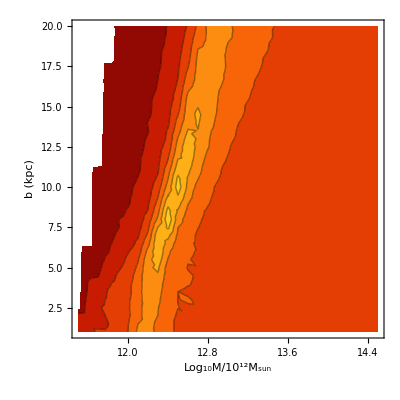

```mathematica
<<KL10x5000logM2D.mx
ListContourPlot[KLStats,Axes->True,AxesOrigin->{Log10[12.2 toSolarMasses],8.0},PlotRange->{0.05,0.75},Contours->Range[0.05,0.75,0.1],ColorFunction->"SolarColors",FrameStyle->Directive[FontFamily->"Helvetica",FontSize->20],Axes->True,AxesStyle->Thick,FrameLabel->{"Log_10M/10^12M_sun","b (kpc)"}]
```